# Studio di funzioni: supporto all’insegnamento

## Sebastian Davrieux Francesco Trombi

## Introduzione

Il seguente notebook è stato creato con l’intento di fornire un supporto concreto all’insegnamento dell’analisi matematica, in particolare per quanto riguarda lo studio di funzioni, per docenti delle Scuole Secondarie Superiori.

Tale strumento fornirà dunque aiuti visuali, che mostrino agli studenti sia le motivazioni che determinano ogni passaggio dello studio di funzione, sia i risultati che tali passaggi comportano.
Questo strumento non vuole dunque porsi come una semplice “calcolatrice”, ma come complemento alle lezioni ed alle esercitazioni in classe.

Funzionamento

Innanzitutto è opportuno indicare il funzionamento di tale strumento.

## Studio di funzione

Studio del dominio

Il dominio è l’insieme di definizione di una funzione. In altre parole, definisce un sottoinsieme dello spazio in cui ha senso valutare la funzione. Nel suo calcolo è necessario tenere a mente che:
- se ci sono denominatori vanno posti diversi da zero;
- se ci sono logaritmi, i loro argomenti vanno posti strettamente maggiori di zero;
-

Studio di parità e disparità

Studiare la parità o la disparità di una funzione può rivelarsi estremamente utile, soprattutto in vista del disegno del grafico.
Se una funzione è pari, allora è simmetrica rispetto all’asse delle y.
Se una funzione è dispari, allora è simmetrica rispetto all’origine degli assi (0, 0).
In una di queste due eventualità il lavoro di disegno del grafico verrebbe dimezzato.

Una funzione f è pari se:
		f ( - x ) = f ( x );
una funzione f è dispari se:
		f ( - x ) = - f ( x ).
		
Una funzione può dunque essere pari o dispari o nessuna delle due.

Intersezione con gli assi

Sapere dove la funzione f interseca gli assi serve a garantire interseca gli assi serve a garantire dei buoni punti di riferimento per cominciare a disegnare il grafico di funzione.

### Intersezione con l’asse delle x

Poniamo f ( x ) = 0 e risolviamo questa equazione, in cui vediamo i valori di x per cui f ( x ) si annulla, intersecando l’asse delle x.

### Intersezione con l’asse delle y

Si calcola f ( 0 ), dunque si calcola y = f ( 0 ).
Facendo così possiamo vedere se e a quale valore di ordinata la funzione passa per l’asse delle oridnate, che ha equazione x = 0.

Ricorda: ci possono essere una, più o nessuna intersezione con l’asse delle ascisse, mentre ci possono essere o una o nessuna intersezione con l’asse delle ordinate.

Studio del segno

Studiare il segno della funzione serve a capire dove la funzione è positiva o negativa, dunque in quali intervalli del dominio il grafico si trova al di sopra dell’asse delle ascisse e dove al di sotto.
Nelle intersezioni con l’asse delle x la funzione cambia ovviamente di segno.

Per conoscere il segno di una funzione f, basta risolvere la disequazione:
		f ( x ) > 0.
		
Ricorda: le soluzioni da prendere in considerazione devono rientrare nel dominio della funzione.

Limiti agli estremi del dominio

Derivata prima, massimi e minimi, monotonia

Derivata seconda, convessità e punti di flesso

Grafico della funzione

## Conclusioni

## Studio della funzione f(x) = ((x-1)/(x-2))e^(x-1)

(Ricordatevi di ripulire le variabili f, x, e che la costante "e" vuole la maiuscola in Mathematica).

```mathematica
Clear[f,x];
```

```mathematica
f[x_]:= ((x-1)/(x-2))E^(x-1);
```

Determinare: dominio, grafico, limiti, asintoti, zeri, massimi, minimi, crescenza, decrescenza, flessi. Disegnare la tangente nel punto di flesso.

Dominio: tutti i numeri reali tranne x=2

Grafico. Modificate il dominio della y (comando PlotRange -> {y1,y2}) in modo da rendere il grafico più comprensibile.

```mathematica
red = RGBColor[1,0,0]; 
yellow =  RGBColor[1,1,0]; 
blue =  RGBColor[0,0,1];
```

```mathematica
Plot[f[x], {x, -1, 3}, PlotStyle -> red, PlotRange -> {-10, 30}, ImageSize->700];
```

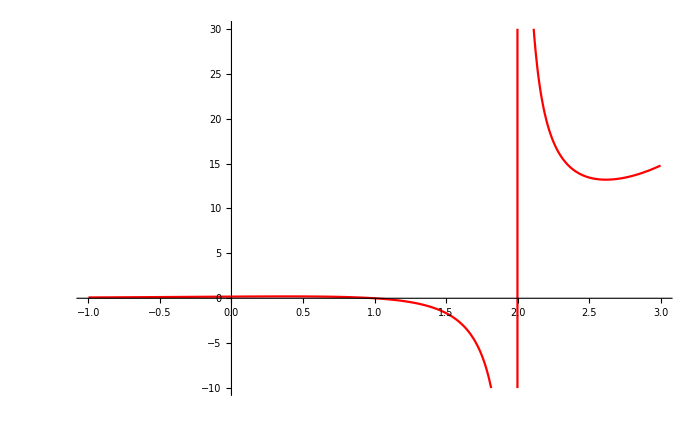

```mathematica
%6
```

Limiti agli estremi del dominio: Calcolate i limiti per x-> -∞, x->2-, x->2+, x->+∞.

```mathematica
Limit[f[x], x -> -∞]
```

```mathematica
Limit[f[x], x -> 2,Direction->1]
```

```mathematica
Limit[f[x], x -> 2,Direction->-1]
```

```mathematica
Limit[f[x], x -> +∞]
```

Zeri. f[x]=0 se e solo se (x-1)=0. Dunque l'unico zero è in x=1. Controlliamo risolvendo f[x]=0 meccanicamente (con Reduce, opp. Solve, opp. FindRoot).

```mathematica
Solve[f[x]==0,{x}]
```

Segni. f[x] è continua, dunque il suo segno non cambia in un intervallo in cui sia sempre definita e non abbia zeri. Ne segue che il segno di f[x] è costante:
 in ]-∞,1[ (dato che x=1 è uno zero di f[x]) 
 in ]1,2[    (dato che x=2 è un punto di non definizione)
 in ]2,+∞[.
  In questi intervalli, il segno si determina calcolando f[x] in un qualsiasi punto dell'intervallo. Da -∞ a 1 la f è positiva, da 1 a 2 è negativa, da 2 in poi positiva.

Asintoti. C'è un asintoto orizzontale y=0 in x=-∞, un asintoto verticale in x=2. Non c'è nessun asintoto obliquo per x->+∞: la pendenza di tale asintoto dovrebbe essere il limite di f[x]/x per x->+∞, ma tale limite è +∞.

```mathematica
Limit[f[x]/x, x -> +Infinity]
```

Massimi e minimi, crescenza e decrescenza. Innanzitutto disegnamo ingranditi i comportamenti della funzione tra -4 e 2, e tra 2 e 4.

```mathematica
Plot[f[x],{x,-4,1.5}, 
	PlotStyle->red, 
	ImageSize->700]
```

In [-∞,2] risulta evidente un andamento crescente e concavo da -∞ fino a circa -0.5. L'andamento della funzione è quindi crescente e convesso, con un massimo all'incirca in +0.5. Poi f[x] decresce fino a x=+2, y=-∞. Queste impressioni dovranno venire confermate con lo studio della derivata prima e seconda di f.

```mathematica
Plot[f[x],{x,2,4}, PlotStyle->red,ImageSize->700]
```

In [2,∞] vediamo un andamento convesso, prima decrescente poi crescente, con un minimo circa in x=+2.5.

Per calcolare i massimi e i minimi, studiamo f'[x], e risolviamo l'equazione f'[x]=0 in vicinanza di x=+0.5,+2.5. Gli zeri di f'[x] corrispondono a massimi, minimi e flessi orizzontali di f[x].
 Per stabilire se uno zero di f'[x] è un massimo, minimo o flesso, dobbiamo studiare il segno di f'[x]. Di nuovo, usiamo il fatto che f'[x] è continua e quindi non cambia segno in un intervallo in cui è sempre definita e non ha zeri. 
 f'[x]>0 significa f crescente in x, mentre f'[x]<0 significa f decrescente in x. Un x tale che f'[x]=0 è un massimo se f è crescente prima di x e decrescente dopo, un minimo se f è decrescente prima di x, e crescente dopo, un flesso altrimenti.

```mathematica
f'[x]
```

Semplifichiamo l'espressione per f'[x].

```mathematica
Simplify[f'[x]]
```

Disegnamo f'[x]. Per meglio rappresentare f'[x], è bene disegnare separatamente il grafico prima e dopo il polo x=2.

```mathematica
Plot[f'[x],{x,-2,1},
	PlotStyle->yellow, ImageSize->700]
```

```mathematica
Plot[f'[x],{x,2,4},PlotRange->{-10,10},PlotStyle->yellow]
```

L'andamento di f'[x]. Vediamo un massimo in -0.5 circa, un segno positivo fino a uno zero in +0.5 circa, quindi un andamento negativo fino ad uno zero in +2.5 circa. Ne segue che f[x] è crescente fino a circa -0.5, decrescente fino a +2.5, quindi di nuovo crescente. Il primo zero di f'[x] sarà quindi un massimo di f[x], il secondo un minimo

Calcolo del Massimo.  Il primo zero di f'[x] corrisponde a un massimo di f[x]. Troviamone il valore (con Reduce opp. Solve opp. FindRoot).

```mathematica
FindRoot[f'[x] == 0, {x,0.5}]
```

Calcolo del Minimo. Il secondo zero di f'[x] corrisponde a un minimo di f[x].

```mathematica
FindRoot[f'[x] == 0, {x,2.5}]
```

Concavità, Convessità, Flessi. Infine, individuiamo concavità, convessità e flessi obliqui di f[x] studiando f''[x]. Di nuovo, studiamo prima gli zeri di f''[x], poi, usando il fatto che f''[x] è continua, il segno di f''[x]. Quando f''[x]<0, allora f[x] ha concavità verso in basso (è convessa). Quando f''[x]>0, allora f[x] ha concavità verso l'alto (è concava). Quando f''[x]=0, allora f[x] ha un flesso ascendente (un punto, cioè, in cui la tangente ad f[x] "trapassa" il grafico di f[x]).

Calcoliamo f''[x].

```mathematica
Simplify[f''[x]]
```

Disegnamo f''[x].

```mathematica
Plot[f''[x],{x,-1,1},PlotStyle->blue]
```

Calcolo del Flesso e della sua pendenza. f''[x] è negativa prima di (circa) -0.3, poi nulla, poi positiva. Dunque f[x] ha prima concavità verso il basso, poi un flesso in -0.3 circa, poi concavità verso l'alto. Troviamo l'unico x0 tale che f''[x0]=0.

```mathematica
FindRoot[f''[x]==0,{x,0.5}]
```

Il valore x0 trovato è un flesso obliquo, di coordinate (x0,y0) con y0 =f[x0], e pendenza (inclinazione della tangente ad f[x] in x0) pari a m0=f'[x0]. Definiamo x0, y0, m0.

```mathematica
x0 = -0.269530832783464457;
```

```mathematica
y0 = f[x0]
```

```mathematica
m0 = f'[x0]
```

Disegno della tangente nel punto di flesso. L'unica retta che passi per (x0,y0), e che abbia pendenza m0, è y=m0(x-x0)+y0. Disegnamo simultaneamente f[x] e la sua tangente in x0.
   Verifichiamo che x0 è  un flesso (la tangente in x0 è prima sotto il grafico di f[x], poi lo attraversa in x0, infine si trova al di sopra di esso).

```mathematica
Plot[{f[x],m0*(x-x0)+y0},{x,-2,1.2},PlotStyle->{red,blue}, ImageSize->700]
```

## Studio della funzione g(x) = x-3Log[x]-1.1^x

Ricordatevi di ripulire le variabili g, x.

```mathematica
Clear[g,x];
g[x_]:=x-3Log[x]-1.1^x;
```

Determinare per y=g(x): dominio, grafico, limiti, asintoti, zeri, massimi, minimi, crescenza, decrescenza, flessi. Disegnare la tangente negli eventuali punti di flesso.

Il dominio è ]0,∞[ (a causa della presenza di Log[x]). Disegnamo il grafico di g(x).

```mathematica
red = RGBColor[1,0,0];
yellow= RGBColor[1,1,0];
blue = RGBColor[0,0,1];
```

```mathematica
Plot[g[x],{x,0,40},
	PlotRange->{-5,10},
	PlotStyle->red,
ImageSize->700]
```

Il grafico evidenza:
- un asintoto verticale in x=0;
- una decrescenza con uno zero, circa in  1;
- un minimo negativo, circa in 4;
- una crescenza con un nuovo zero, circa in 9;
- una concavità verso l'alto fino a circa 14;
- quindi un flesso (cambiamento di concavità, ora rivolta verso il basso);
- un massimo intorno a 24;
- una decrescenza con uno zero intorno a 32;
- infine una tendenza a -∞.
Tutte queste informazioni andranno controllate e precisate con lo studio di g'(x) ed g''(x).

Zeri. Cerchiamo gli zeri di g(x) con il metodo di Newton (comando Root). Confermiamo i tre zeri sopra descritti.

```mathematica
FindRoot[g[x]==0,{x,1}]
```

```mathematica
FindRoot[g[x]==0,{x,10}]
```

```mathematica
FindRoot[g[x]==0,{x,30}]
```

Segni di g. g[x] è continua, dunque il suo segno non cambia in un intervallo in cui sia sempre definita e non abbia zeri. Ne segue che il segno di g[x] è costante:
 in ]0.00, 0.95[    (dato che x=0.95 circa è uno zero di g[x]) 
 in ]0.95, 8.88[    (dato che x=8.88 circa è uno zero di g[x])
 in ]8.88, 32.4[    (dato che x=32.4 circa è uno zero di g[x])
 in ]32.4, +∞ [    
  In questi intervalli, il segno si determina calcolando g[x] in un qualsiasi punto dell'intervallo. Da 0.00 a  0.95 la g è positiva, da 0.95 a 8.88 è negativa, da 8.88, 32.4 è di nuovo positivia, da 32.4 in poi positiva.

Studiamo il comportamento di di g(x) agli estremi del dominio: confermiamo l'asintoto verticale in x=0.

```mathematica
Limit[g[x],x->0]
```

Studiamo il comportamento per x→∞.

```mathematica
Limit[g[x],x->∞]
```

Non tutte le versioni di Mathematica sono grado di calcolare l'ultimo limite. In base a considerazioni sugli ordini di infinito (-1.1^x è un esponenziale, quindi prevale sugli altri), noi possiamo comunque stabilire che tale limite è -∞.

Calcoliamo la derivata g'[x] di g[x].

```mathematica
g'[x]
```

Disegnamo il grafico di g'[x], calcoliamone il valore agli estremi del dominio.

```mathematica
Plot[g'[x],{x,0,40},
	PlotStyle->blue,
ImageSize->700]
```

Studiamo i limiti di g' agli estremi del dominio.

⁃Graphics⁃

```mathematica
Limit[g'[x],x->0]
```

```mathematica
Limit[g'[x],x->∞]
```

Il primo risultato conferma che x=0 è un asse verticale di g. Il secondo stabilisce che non esistono asintoti obliqui di g (dovrebbero avere pendenza Lim[g'[x],x->∞] = -∞).

Infine, troviamo i due zeri di g'[x] (che sono, nell'ordine, un punto di minimo e massimo locali di g[x]).

```mathematica
FindRoot[g'[x]==0,{x,5}]
```

```mathematica
FindRoot[g'[x]==0,{x,25}]
```

Segni di g'. g'[x] è continua. Ripetendo il ragionamento già utilizzato per g[x], possiamo osservare che g' non cambia segno in un intervallo in cui sia definita e non abbia zeri. Ne segue che il segno di g'[x] è costante:
 in ]0.00, 3.45[    (dato che x=3.45 circa è uno zero di g'[x]) 
 in ]3.45, 23.2[    (dato che x=23.2 circa è uno zero di g'[x])
 in ]23.2, +∞ [    
 Di conseguenza g' sarà negativa in ]0.00, 3.45[, positiva in ]3.45, 23.2[, negativa in ]23.2, +∞ [. g sarà quindi decrescente in ]0.00, 3.45[, decrescente in ]3.45, 23.2[, crescente in ]23.2, +∞ [. Dunque 3.45 sarà un minimo, e 23.2 un massimo (locali).

Concavità, Convessità, Flessi. Ripetiamo il calcolo dei limiti, il disegno del grafico ed il calcolo degli zeri per g''[x]. Quando g''[x]<0 avremo una concavità verso il basso per g, quando g''[x]=0 avremo un flesso, quando g''[x]>0 avremo una concavità verso l'alto.

```mathematica
g''[x]
```

```mathematica
Limit[g''[x],x->0]
```

```mathematica
Limit[g''[x],x->∞]
```

```mathematica
Plot[g''[x],{x,0,40},
	PlotRange->{-1,1},
	PlotStyle->yellow,
ImageSize->700]
```

```mathematica
FindRoot[g''[x],{x,10}]
```

L'unica soluzione x0 di g''[x]=0 è un punto di flesso di g[x]. Il punto ha coordinate (x0,y0), con y0=g[x0], e tangente a g[x] di pendenza m0=g'[x0].

```mathematica
x0 = 10.8407192737551527;
y0 = g[x0]
m0 = g'[x0]
```

Disegnamo ora sovrapposti il grafico di g[x] e il flesso (la tangente ad g[x] in x=x0). Tale tangente è l'unica retta per (x0,y0) di pendenza m, dunque ha equazione y=m0(x-x0)+y0.

```mathematica
Plot[{g[x],m0(x-x0)+y0},{x,0,40},
	PlotRange->{-5,10},
	PlotStyle->{red,blue},
ImageSize->700]
```

## Studio delle funzioni: f(x) = (x^2+2x-3)/(5x^2+x) g(x) = √x*|log(x)|

Includiamo altri due esempi di funzioni da studiare, questa volta senza dare nessun suggerimento (tranne questo: ricordatevi di ripulire i nomi di funzioni f, g prima di usarli).

### f(x) = (x^2+2x-3)/(5x^2+x)

```mathematica
Clear[f];
```

```mathematica
f[x_]:=(x^2+2x-3)/(5x^2+x);
```

```mathematica
red = RGBColor[1,0,0];
yellow= RGBColor[1,1,0];
green= RGBColor[0,1,0];
blue = RGBColor[0,0,1];
```

```mathematica
Plot[f[x],{x,-10,10},PlotStyle->red,ImageSize->700,PlotRange->{-1,1}]
```

```mathematica
Plot[f[x],{x,-1,1},PlotStyle->red,ImageSize->700,PlotRange->{-50,200}]
```

```mathematica
Plot[f[x],{x,2,5},PlotStyle->red,ImageSize->700]
```

```mathematica
Reduce[f[x]==0,x]
```

```mathematica
Reduce[(5x^2+x)==0,x]
```

```mathematica
Limit[f[x],x->-Infinity]
```

```mathematica
Limit[f[x],x->-1/5,Direction->+1]
Limit[f[x],x->-1/5,Direction->-1]
```

```mathematica
Limit[f[x],x->0,Direction->+1]
Limit[f[x],x->0,Direction->-1]
```

```mathematica
Limit[f[x],x->+Infinity]
```

```mathematica
f'[x]
```

```mathematica
Simplify[f'[x]]
```

```mathematica
Reduce[f'[x]==0]
```

```mathematica
N[Reduce[f'[x]==0]]
```

```mathematica
f''[x]
```

```mathematica
Simplify[f''[x]]
```

```mathematica
Reduce[f''[x]==0]
```

```mathematica
N[Reduce[f''[x]==0]]
```

```mathematica
Plot[f[x],{x,-20,20},PlotStyle->red,ImageSize->700,PlotRange->{0.1,0.3}]
```

### g(x) = √x*|log(x)|

```mathematica
Clear[g];
```

```mathematica
g[x_] := Sqrt[x]*If[Log[x]>0,Log[x],-Log[x]]
```

```mathematica
red = RGBColor[1,0,0];
yellow= RGBColor[1,1,0];
green= RGBColor[0,1,0];
blue = RGBColor[0,0,1];
```

```mathematica
Plot[g[x],{x,0,2},PlotStyle->red,ImageSize->700]
```

```mathematica
Plot[g[x],{x,0,20},PlotStyle->red,ImageSize->700]
```

```mathematica
g'[x]
```

```mathematica
Simplify[g'[x]]
```

```mathematica
Plot[g'[x],{x,0,2},PlotStyle->yellow,ImageSize->700]
```

```mathematica
Limit[g'[x],x->1]
```

```mathematica
Plot[g''[x],{x,0,2},PlotRange->{-1,1},ImageSize->700,PlotStyle->blue]
```

```mathematica
Plot[Abs'[x],{x,-1,1},PlotStyle->blue,ImageSize->700]
```